```mathematica
SetDirectory["/uni-mainz.de/homes/asourpis/Documents/gromer/PhD_roadmap/MD&electricfield"];
```

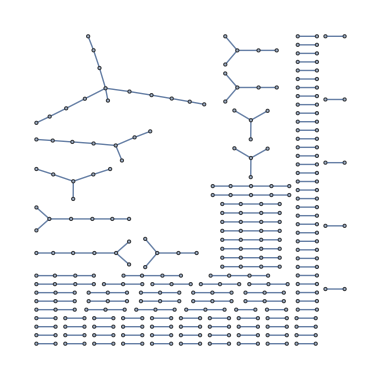

122

```mathematica
data21ns=Import["vmd_hbonds.csv"];
gintertest=Graph[data21ns];
edl21ns=EdgeList[gintertest];
g1=Graph[edl21ns]//Table
g11=Labeled[g1,"t=21ns",Top];
size=Length[ConnectedComponents[g1]]
(*dir21ns=CreateDirectory["21"];
Do[Export["21/ntw_clusters"<>ToString[n]<>".txt",ConnectedComponents[g1][[n]]],{n,1,size}];*)
```

```mathematica
data21ns=Import["hbonds.csv"];
gintertest=Graph[data21ns];
edl21ns=EdgeList[gintertest];
g1=Graph[edl21ns]//Table
g11=Labeled[g1,"t=21ns",Top];
size=Length[ConnectedComponents[g1]]
```

Import::nffil: File hbonds.csv not found during Import.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[$Failed]].

Graph[EdgeList[Graph[$Failed]]]

ConnectedComponents::graph: A graph object is expected at position 1 in ConnectedComponents[Graph[EdgeList[Graph[$Failed]]]].

1

```mathematica
a=FindFundamentalCycles[g1]
```

{{1523<->1551,1551<->1510,1510<->1523},{1599<->1614,1614<->1365,1365<->1416,1416<->1568,1568<->1427,1427<->1343,1343<->1433,1433<->1409,1409<->1386,1386<->1513,1513<->1439,1439<->1503,1503<->1271,1271<->1219,1219<->1454,1454<->1293,1293<->1248,1248<->1443,1443<->1599},{1601<->1546,1546<->1534,1534<->1293,1293<->1454,1454<->1219,1219<->1271,1271<->1503,1503<->1439,1439<->1513,1513<->1386,1386<->1224,1224<->1279,1279<->1609,1609<->1394,1394<->1370,1370<->1491,1491<->1425,1425<->1327,1327<->1533,1533<->1481,1481<->1384,1384<->776,776<->1451,1451<->1341,1341<->1450,1450<->1423,1423<->1601},{1605<->1580,1580<->1415,1415<->1421,1421<->1605},{578<->1467,1467<->1282,1282<->1333,1333<->1323,1323<->1586,1586<->1398,1398<->1446,1446<->578},{1545<->1467,1467<->1282,1282<->1333,1333<->1323,1323<->1586,1586<->1398,1398<->1545},{1508<->1524,1524<->1477,1477<->1333,1333<->1515,1515<->1508},{1510<->1551,1551<->1563,1563<->1370,1370<->1491,1491<->1425,1425<->1327,1327<->1510},{1436<->1567,1567<->1506,1506<->1229,1229<->1319,1319<->1436},{1532<->1345,1345<->1558,1558<->1561,1561<->1406,1406<->1427,1427<->1343,1343<->1433,1433<->1409,1409<->1386,1386<->1513,1513<->1439,1439<->1503,1503<->1271,1271<->1219,1219<->1346,1346<->1266,1266<->1393,1393<->1310,1310<->1532},{1573<->1425,1425<->1491,1491<->1370,1370<->1394,1394<->1609,1609<->1279,1279<->1224,1224<->1386,1386<->1269,1269<->1350,1350<->1488,1488<->1573},{1439<->1513,1513<->1386,1386<->1269,1269<->1290,1290<->1439},{1488<->1350,1350<->1269,1269<->1290,1290<->1488},{1465<->1496,1496<->1234,1234<->1576,1576<->1280,1280<->1465},{1510<->1551,1551<->1563,1563<->1370,1370<->1491,1491<->1425,1425<->1278,1278<->1510},{1327<->1425,1425<->1278,1278<->1327},{1454<->1219,1219<->1271,1271<->1385,1385<->1454},{1486<->1400,1400<->1353,1353<->1600,1600<->1543,1543<->1257,1257<->1486},{1534<->1293,1293<->1248,1248<->1492,1492<->1534},{1345<->1558,1558<->1561,1561<->1406,1406<->1427,1427<->1343,1343<->1433,1433<->1409,1409<->1386,1386<->1513,1513<->1439,1439<->1503,1503<->1271,1271<->1219,1219<->1454,1454<->1293,1293<->1345},{1437<->1278,1278<->1425,1425<->1491,1491<->1370,1370<->1563,1563<->1551,1551<->1523,1523<->1352,1352<->1247,1247<->1437},{1261<->1413,1413<->1545,1545<->1467,1467<->1282,1282<->1333,1333<->1323,1323<->1586,1586<->1398,1398<->1446,1446<->1237,1237<->1261},{1394<->1609,1609<->1279,1279<->1224,1224<->1394},{1561<->1406,1406<->1427,1427<->1343,1343<->1433,1433<->1409,1409<->1386,1386<->1513,1513<->1439,1439<->1503,1503<->1271,1271<->1219,1219<->1346,1346<->1561},{1406<->1427,1427<->1343,1343<->1433,1433<->1409,1409<->1386,1386<->1513,1513<->1439,1439<->1503,1503<->1271,1271<->1406}}

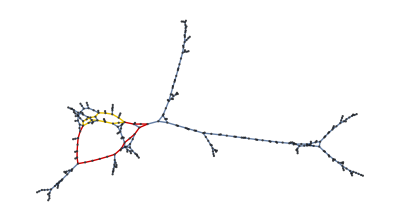

```mathematica
HighlightGraph[g1,{a[[3]],a[[20]]}]
```

```mathematica
a[[3]]
```

{1601<->1546,1546<->1534,1534<->1293,1293<->1454,1454<->1219,1219<->1271,1271<->1503,1503<->1439,1439<->1513,1513<->1386,1386<->1224,1224<->1279,1279<->1609,1609<->1394,1394<->1370,1370<->1491,1491<->1425,1425<->1327,1327<->1533,1533<->1481,1481<->1384,1384<->776,776<->1451,1451<->1341,1341<->1450,1450<->1423,1423<->1601}

```mathematica
List[a[[3]]]
```

{{1601<->1546,1546<->1534,1534<->1293,1293<->1454,1454<->1219,1219<->1271,1271<->1503,1503<->1439,1439<->1513,1513<->1386,1386<->1224,1224<->1279,1279<->1609,1609<->1394,1394<->1370,1370<->1491,1491<->1425,1425<->1327,1327<->1533,1533<->1481,1481<->1384,1384<->776,776<->1451,1451<->1341,1341<->1450,1450<->1423,1423<->1601}}

```mathematica
data21ns
```

{{1218,204},{1219,1271},{1219,1346},{1221,1208},{1221,1577},{1222,1528},{1224,1168},{1224,1386},{1228,1021},{1228,1323},{1229,1181},{1229,1506},{1230,40},{1230,1246},{1234,1304},{1234,1610},{1235,356},{1235,1296},{1237,1261},{1237,1284},{1239,1110},{1239,1470},{1241,1377},{1245,369},{1245,1374},{1246,1381},{1247,1437},{1247,1572},{1248,1293},{1248,1492},{1251,739},{1251,1449},{1253,1300},{1256,991},{1256,1499},{1257,1486},{1259,1367},{1261,1413},{1265,1218},{1265,1390},{1266,459},{1266,1393},{1269,1209},{1269,1350},{1270,1520},{1271,1385},{1271,1503},{1273,1328},{1275,1153},{1275,1424},{1278,1425},{1279,1224},{1280,1606},{1282,1467},{1284,512},{1284,1357},{1290,1269},{1290,1488},{1293,1345},{1293,1454},{1296,235},{1299,1230},{1300,3},{1310,1393},{1310,1616},{1311,441},{1319,1229},{1319,1414},{1323,1333},{1323,1586},{1327,412},{1327,1278},{1327,1425},{1328,1409},{1330,1412},{1333,1282},{1333,1515},{1334,862},{1334,1531},{1336,1265},{1336,1507},{1340,1595},{1341,1451},{1341,1500},{1343,1077},{1343,1427},{1344,1482},{1345,1532},{1346,1266},{1346,1561},{1350,1488},{1352,1247},{1352,1458},{1353,1389},{1353,1600},{1357,1163},{1357,1230},{1359,1256},{1359,1469},{1360,567},{1360,1389},{1364,272},{1365,1529},{1367,1471},{1368,1253},{1370,1394},{1370,1563},{1372,1253},{1372,1455},{1373,1359},{1374,1479},{1374,1578},{1375,581},{1375,1364},{1377,1344},{1377,1585},{1378,782},{1379,1340},{1379,1456},{1381,645},{1381,969},{1382,294},{1382,1228},{1384,776},{1384,1481},{1385,1113},{1386,1269},{1386,1513},{1389,689},{1390,1239},{1392,1300},{1392,1375},{1393,1235},{1394,1224},{1394,1609},{1395,1372},{1398,1446},{1399,1545},{1400,1353},{1404,1432},{1404,1511},{1406,1271},{1406,1427},{1408,1506},{1409,1386},{1409,1433},{1413,723},{1413,1545},{1414,932},{1414,1103},{1415,1245},{1415,1580},{1416,1365},{1416,1547},{1417,445},{1417,1464},{1421,1415},{1421,1605},{1423,1450},{1423,1601},{1424,1500},{1425,1491},{1425,1573},{1427,262},{1427,1568},{1431,425},{1432,542},{1432,1455},{1433,1343},{1433,1541},{1435,1187},{1436,1319},{1437,692},{1437,1278},{1439,1290},{1443,283},{1443,1248},{1444,1473},{1444,1485},{1445,1521},{1445,1617},{1446,578},{1446,1237},{1449,920},{1450,980},{1450,1341},{1451,776},{1452,1059},{1452,1270},{1454,1219},{1454,1385},{1455,825},{1456,1246},{1456,1378},{1458,199},{1458,1311},{1461,604},{1464,1477},{1465,1280},{1466,1373},{1466,1452},{1467,152},{1467,578},{1469,396},{1470,1571},{1471,1435},{1473,1621},{1476,1392},{1476,1607},{1477,1333},{1479,301},{1479,1377},{1481,1533},{1485,775},{1486,1400},{1488,1461},{1488,1573},{1491,1370},{1495,1466},{1496,1234},{1496,1465},{1499,1214},{1499,1261},{1500,154},{1500,1304},{1503,1439},{1503,1539},{1504,175},{1504,1495},{1506,458},{1506,1567},{1507,1509},{1508,1524},{1509,832},{1509,1241},{1510,1278},{1510,1327},{1511,147},{1513,1439},{1514,1336},{1515,790},{1515,1508},{1516,98},{1516,752},{1520,1251},{1521,1535},{1522,530},{1522,1612},{1523,1352},{1523,1510},{1524,1477},{1527,1275},{1528,1511},{1529,1012},{1531,1587},{1532,1310},{1533,1327},{1533,1600},{1534,1293},{1534,1492},{1535,101},{1539,533},{1541,483},{1541,1431},{1542,473},{1542,1482},{1543,1257},{1545,1398},{1545,1467},{1546,1330},{1546,1534},{1547,153},{1551,1510},{1551,1523},{1556,807},{1556,1576},{1558,1345},{1561,1406},{1561,1558},{1563,1551},{1567,1436},{1567,1522},{1568,1416},{1571,859},{1571,1417},{1573,476},{1573,1183},{1576,1234},{1576,1280},{1577,1612},{1578,132},{1580,990},{1580,1605},{1586,1398},{1587,1516},{1587,1542},{1595,206},{1595,623},{1599,80},{1599,1443},{1600,1543},{1601,1546},{1605,421},{1605,1408},{1606,1259},{1606,1473},{1607,1221},{1609,1279},{1609,1421},{1612,277},{1613,1423},{1614,1365},{1614,1599},{1616,685},{1617,1340},{1620,861},{1620,1368}}

```mathematica
StringJoin[ToString/@Riffle[list," "]]
```